```mathematica
(* p.45 of 2014/15 catalog discusses feedback current into amplifier *)
```

## Task Parameters and Functions

```mathematica
w0 = 14 60/(2π); (* required speed - rpm *)
N0 = 4*1000; (* required torque - mNm *)
wd = 75;1.2 w0; (* safety factor - rpm *)
Nd = 7000;1.2 N0; (* safety factor - mNm *)
Ibat = 30; (* max current from batteries - A *)
Pd = wd Nd 2 π/60/1000; (* max mechanical power - W *)
period = 1/50000; (* Hz *)
```

```mathematica
SpeedTorqueCurve::TimeConstant = "period is too short given how quickly the motor wires heat up.";
SpeedTorqueCurve[G_:1, Tamb_:25, ep_:{}] := Module[{wnl, D, w, n, f, g, h, op, ops, b},
If[period > 5 Ttc, Message[SpeedTorqueCurve::TimeConstant]];

f=Join[{#,Null}&/@FindDivisions[{#1, #2},50],{#,NumberForm[N[#/km/G],{5,1}]}&/@FindDivisions[{#1, #2},10]]&;

g = Append[Thread[Most@MaxSpeed[n, G, Tamb] == {w, D}],   n ≥ 0];
g=Join@@Table[{w, Round[100 D]} /. NSolve[g, {n, w}], {D, 0.1, 1,  0.1}];

h = If[NumericQ[#], #, 0]&;

wnl = kn Vnom/G; (* no-load speed - rpm *)
op = Tooltip[Point[{N0, w0}], "Operating Point"];
ops = Tooltip[Point[{Nd, wd}], "Operating Point with Safety Factor"];
b = Tooltip[Line[{{G km Ibat, 0}, {G km Ibat, wmax}}], "Max Battery Current"];

Plot[{wnl - (s / G^2) N, First@MaxSpeed[N, G, Tamb], h@First@MaxSpeed[N/2, G, Tamb]}, {N, 0, G Nstall},
PlotStyle->{{Thick, Blue}, {Thick, Red}, {Thick, Gray}}, PlotLegends->Placed[{"Speed-Torque Curve at Vnom","Continuous Operation", "Dangerous Operation"},Above],Epilog-> {PointSize[Large], op, Thick, b,Purple, ops, ep}, AxesOrigin->{0,0}, Frame->True,FrameLabel->{"Torque (mNm)","Speed (rpm)","Current (A)", "Duty Cycle (%)"}, FrameTicks->{{Automatic,g},{Automatic,f}},ImageSize->Full, Filling->{2-> Axis, 3-> Top}]
];

MaxSpeed[N_, G_:1, Tamb_:25] := Module[{d, t, Vrms, T0, wnl, w},
(* computes maximum speed based on maximum winding temperature and *) (* maximum permissible speed.  The formulas are given in the Maxon *) (* motor catalog based on Vrms and Irms values, where Irms = Inom Sqrt[D] *)  (* for a PWM pulse train with duty cycle D = d^2. *)

T0 = 25;  (* temperature test condition - Celsius *)
wnl = kn Vnom/G; (* no-load speed - rpm *)
t = Sqrt[(Tmax-Tamb)/(Tmax - T0)]; (* temperature correction term *)
d = t G km Inom/N; (* sqrt of duty cycle *)
Vrms = Vnom d; (* rms voltage - V *)
wnl = kn Vrms/G; (* no-load speed - rpm *)
w = wnl - (s/G^2)N;
If[w > wmax, w = wmax];
If[w < 0, w = None];

{w, d^2, Vrms}
];

OverLoad[Imot_, Tmot_] := Module[{T0, K, ton},
(* Tmot is temperature of housing + winding of motor *)
T0 = 25;
K = Imot/Inom Sqrt[(Tmax-T0)/(Tmax - Tmot) Rth1/(Rth1+Rth2)];
ton = Ttc Log[K^2/(K^2-1)];
(* seconds, ratio K ~ Imot/Inom *)
{If[K < 1, ∞, ton], K}
];
```

## EC 90 flat -- 48 V

```mathematica
kn = 44; (* speed coNstalltant - rpm/V *)
km = 217; (* torque coNstalltant - mNm/A *)
Vnom = 48; (* nominal voltage - V *)
s = 0.462; (* speed/torque gradient - rpm/mNm *)
Nstall = 4570; (* stall torque - mNm *)
wmax = 5000; (* max permissible speed - rpm *)
Nnom = 533; (* nominal torque - mNm *)
Inom = 2.27; (* nominal current - A *)
wnom = 1610; (* nominal speed - rpm *)
Tmax = 125; (* maximum winding temperature - Celsius *)
Ttc = 46; (* thermal time constant of winding - s *)

G =10;
SpeedTorqueCurve[G]
```

```mathematica
Clear[G]
Solve[G Nnom == Nd, G] // N
Block[{kn, Vnom, s, Nd, wd}, Solve[kn Vnom/G - (s / G^2) Nd== wd , G]]
```

## EC 90 flat -- 24 V

```mathematica
kn = 135; (* speed coNstalltant - rpm/V *)
km = 70.5; (* torque coNstalltant - mNm/A *)
Vnom = 24; (* nominal voltage - V *)
s = 0.659; (* speed/torque gradient - rpm/mNm *)
Nstall = 4940; (* stall torque - mNm *)
wmax = 5000; (* max permissible speed - rpm *)
Nnom = 444; (* nominal torque -mNm *)
Inom = 6.06; (* nominal current - A *)
wnom = 2590; (* nominal speed - rpm *)
Tmax = 125; (* maximum winding temperature - Celsius *)
Ttc = 46; (* thermal time constant of winding - s *)

G =11;
SpeedTorqueCurve[G]
```

```mathematica
Clear[G]
Solve[G Nnom == Nd, G] // N
Block[{kn, Vnom, s, Nd, wd}, Solve[kn Vnom/G - (s / G^2) Nd== wd , G]]
```

## EC 60 flat -- 48 V

```mathematica
kn = 83.4; (* speed coNstalltant - rpm/V *)
km = 114; (* torque coNstalltant - mNm/A *)
Vnom = 48; (* nominal voltage - V *)
s = 0.798; (* speed/torque gradient - rpm/mNm *)
Nstall = 5010; (* stall torque - mNm *)
wmax = 6000; (* max permissible speed - rpm *)
Nnom = 319; (* nominal torque - mNm *)
Inom = 2.78; (* nominal current - A *)
wnom = 3490; (* nominal speed - rpm *)
Tmax = 125; (* maximum winding temperature - Celsius *)
Ttc = 40; (* thermal time constant of winding - s *)

G =6;
Show[SpeedTorqueCurve[G], ListPlot[{{0, 3/4kn Vnom/G}, {3/4 G Nstall, 0}}, Joined-> True]]
```

```mathematica
Clear[G]
Solve[G Nnom == Nd, G] // N
Block[{kn, Vnom, s, Nd, wd}, Solve[kn Vnom/G - (s / G^2) Nd== wd , G]]
```

## EC 60 flat -- 24 V

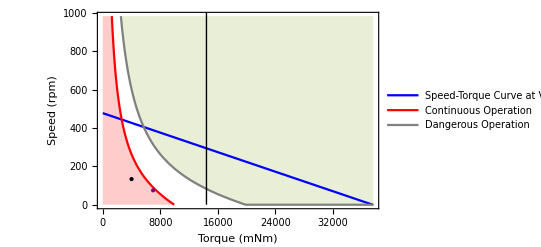

```mathematica
kn = 179; (* speed contant - rpm/V *)
km = 53.4; (* torque constant - mNm/A *)
Vnom = 24; (* nominal voltage - V *)
s = 1.03; (* speed/torque gradient - rpm/mNm *)
Nstall = 4180; (* stall torque - mNm *)
wmax = 6000; (* max permissible speed - rpm *)
Nnom = 289; (* nominal torque - mNm *)
Inom = 5.47; (* nominal current - A *)
wnom = 3740; (* nominal speed - rpm *)
Tmax = 125; (* maximum winding temperature - Celsius *)
Ttc = 40; (* thermal time constant of winding - s *)
Rth1 = 3.5; (* thermal resistance winding-housing - K/W *)
Rth2 = 2.5; (* thermal resistance housing-ambient - K/W *)

G =9;
SpeedTorqueCurve[G]
```

```mathematica
Clear[G]
Solve[G Nnom == Nd, G] // N
Block[{kn, Vnom, s, Nd, wd}, Solve[kn Vnom/G - (s / G^2) Nd== wd , G]]
```

## EC 60 flat -- 12 V

```mathematica
kn = 313; (* speed coNstalltant - rpm/V *)
km = 30.5; (* torque coNstalltant - mNm/A *)
Vnom = 12; (* nominal voltage - V *)
s = 1.32; (* speed/torque gradient - rpm/mNm *)
Nstall = 2850; (* stall torque - mNm *)
wmax = 6000; (* max permissible speed - rpm *)
Nnom = 231; (* nominal torque - mNm *)
Inom = 7.81; (* nominal current - A *)
wnom = 3260; (* nominal speed - rpm *)
Tmax = 125; (* maximum winding temperature - Celsius *)
Ttc = 40; (* thermal time constant of winding - s *)

G =15;
SpeedTorqueCurve[G]
```

```mathematica
Clear[G]
Solve[G Nnom == Nd, G] // N
Block[{kn, Vnom, s, Nd, wd}, Solve[kn Vnom/G - (s / G^2) Nd== wd , G]]
```

## EC 45 flat -- 48 V

```mathematica
kn = 72.7; (* speed coNstalltant - rpm/V *)
km = 131; (* torque coNstalltant - mNm/A *)
Vnom = 48; (* nominal voltage - V *)
s = 3.82; (* speed/torque gradient - rpm/mNm *)
Nstall = 915; (* stall torque - mNm *)
wmax = 10000; (* max permissible speed - rpm *)
Nnom = 134; (* nominal torque -mNm *)
Inom = 0.936; (* nominal current - A *)
wnom = 2540; (* nominal speed - rpm *)
Tmax = 125; (* maximum winding temperature - Celsius *)
Ttc = 178; (* thermal time constant of winding - s *)
Rth1 = 4.1; (* thermal resistance winding-housing - K/W *)
Rth2 = 3.56; (* thermal resistance housing-ambient - K/W *)

G =10;
SpeedTorqueCurve[G]
```

```mathematica
Clear[G]
Solve[G Nnom == Nd, G] // N
Block[{kn, Vnom, s, Nd, wd}, Solve[kn Vnom/G - (s / G^2) Nd== wd , G]]
```

## EC 45 flat -- 30 V

```mathematica
kn = 259; (* speed coNstalltant - rpm/V *)
km = 45.1; (* torque coNstalltant - mNm/A *)
Vnom = 30; (* nominal voltage - V *)
s = 5.44; (* speed/torque gradient - rpm/mNm *)
Nstall = 1170; (* stall torque - mNm *)
wmax = 10000; (* max permissible speed - rpm *)
Nnom = 112; (* nominal torque -mNm *)
Inom = 2.36; (* nominal current - A *)
wnom = 4990; (* nominal speed - rpm *)
Tmax = 125; (* maximum winding temperature - Celsius *)
Ttc = 178; (* thermal time constant of winding - s *)
Rth1 = 4.1; (* thermal resistance winding-housing - K/W *)
Rth2 = 3.56; (* thermal resistance housing-ambient - K/W *)

G =10;
SpeedTorqueCurve[G]
```

```mathematica
Clear[G]
Solve[G Nnom == Nd, G] // N
Block[{kn, Vnom, s, Nd, wd}, Solve[kn Vnom/G - (s / G^2) Nd== wd , G]]
```

## EC 45 flat -- 24 V

```mathematica
kn = 259; (* speed coNstalltant - rpm/V *)
km = 36.9; (* torque coNstalltant - mNm/A *)
Vnom = 24; (* nominal voltage - V *)
s = 4.26; (* speed/torque gradient - rpm/mNm *)
Nstall = 1460; (* stall torque - mNm *)
wmax = 10000; (* max permissible speed - rpm *)
Nnom = 128; (* nominal torque - mNm *)
Inom = 3.21; (* nominal current - A *)
wnom = 4860; (* nominal speed - rpm *)
Tmax = 125; (* maximum winding temperature - Celsius *)
Ttc = 178; (* thermal time constant of winding - s *)
Rth1 = 4.1; (* thermal resistance winding-housing - K/W *)
Rth2 = 3.56; (* thermal resistance housing-ambient - K/W *)

G =10;
SpeedTorqueCurve[G]
```

```mathematica
Clear[G]
Solve[G Nnom == Nd, G] // N
Block[{kn, Vnom, s, Nd, wd}, Solve[kn Vnom/G - (s / G^2) Nd== wd , G]]
```